What is the terminal velocity of a SmartDart?

### from videos you can measure the length of the dart, and compare posiiton in 2 frames

```mathematica
π (0.06/2)^2
```

0.00282743

```mathematica
(*CONSTANTS*)
AreaProj =π (0.06/2)^2 ;(*area of the dart, m^2, 60mm in diameter*)
Cd = 0.47; (*0.47 for sphere, 0.04 for streamlined body, 
1 to 2 for an arrow https://www.researchgate.net/publication/235908721_Aerodynamic_properties_of_an_archery_arrow
*)
m = 0.2; (*kg*)
ρ = 1.225; (*density of air kg/m3*)
g= 9.8; (*m/s2*)
```

```mathematica
Vt =√((2 m g)/(ρ AreaProj Cd)) (*Terminal Velocity, in m/s*)
```

49.0716

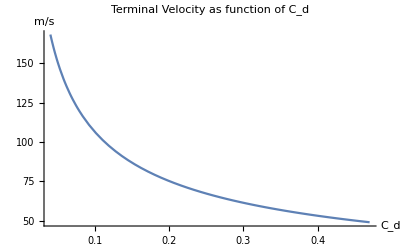

```mathematica
Plot[√((2 m g)/(ρ AreaProj Cd)),{Cd,0.04,0.47},PlotRange->All, AxesOrigin->{0,0},AxesLabel->{"C_d","m/s"},PlotLabel->"Terminal Velocity as function of C_d"]
```

Solve to get velocity as a function of time

```mathematica
DSolve[{v'[t]==b - v[t]^2 a,v[0]==0},v,t] (* a = 1/(2 m) ρ AreaProj Cd, b = g, terminal velocity = (√b)/(√a)*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v→Function[{t},(√b Tanh[√a √b t])/(√a)]}}

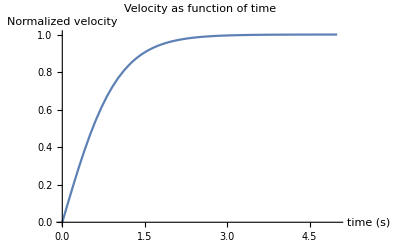

```mathematica
Plot[Tanh[ t],{t,0,5},PlotRange->All,AxesLabel->{"time (s)","Normalized velocity"},PlotLabel->"Velocity as function of time"]
```

Solve to get position as a function of time

```mathematica
DSolve[{p''[t]==b - p'[t]^2 a,p[0]==0,p'[0]==0},p,t]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 1 - Cosh[√a\ √b\ C[1]]^2 == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→Function[{t},Log[Cosh[√a √b t]]/a]},{p→Function[{t},(-ⅈ π+Log[Cosh[√a √b (-(ⅈ π)/(√a √b)+t)]])/a]}}

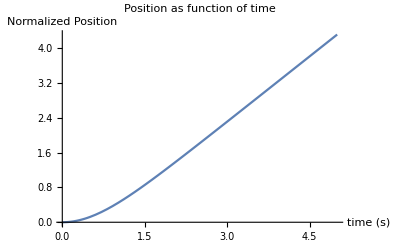

```mathematica
Plot[Log[Cosh[ t]],{t,0,5},AxesLabel->{"time (s)","Normalized Position"},PlotLabel->"Position as function of time"]
```

Falling object reaches 90% speed at time

```mathematica
Solve[Tanh[√a √b t]==9/10,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→ArcTanh[9/10]/(√a √b)}}

Falling object reaches 90% speed when it falls from what height?

```mathematica
FullSimplify[Log[Cosh[√a √b ArcTanh[Perct]/(√a √b)]]/a]
```

-Log[1-Perct^2]/(2 a)

```mathematica
FullSimplify[Log[Cosh[√a √b ArcTanh[9/10]/(√a √b)]]/a]
```

```mathematica
Log[100/19]/(2 a)/.a-> 1/(2 m) ρ AreaProj 0.47
```

204.034

```mathematica
Log[100/19]/(2 a)/.a->  1/(2 m) ρ AreaProj 0.04
```

2397.4

Compare with Cd

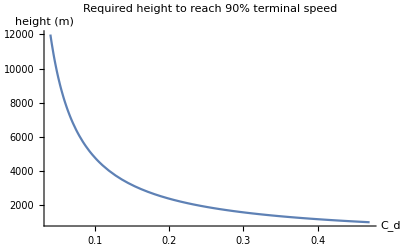

```mathematica
Plot[Log[100/19]/(2 a)/.a-> 1/2 ρ AreaProj Cd,{ Cd,0.04,0.47},PlotRange->All,

PlotLabel->"Required height to reach 90% terminal speed",AxesLabel->{"C_d","height (m)"}]
```

Compare analytic to numeric solution (they match, so no need for numeric solution)

```mathematica
Cd = 1;
```

```mathematica
s=NDSolve[{y''[t]== g -1/(2 m) y'[t]^2 ρ AreaProj Cd,y[0]==0,y'[0]==0},y,{t,0,100}]
```

{{y→InterpolatingFunction[{{0., 100.}}, <>]}}

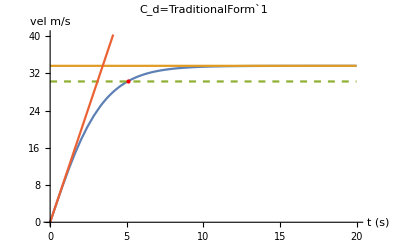

```mathematica
t90 = ArcTanh[9/10]/(√a √b)/.{a->  1/(2 m) ρ AreaProj Cd, b->  g};
Plot[{Evaluate[y'[t]/.s],√((2 m g)/(ρ AreaProj Cd)),0.9*√((2 m g)/(ρ AreaProj Cd)),g t},{t,0,20},PlotRange->{{0,20},{0,1.2 √((2 m g)/(ρ AreaProj Cd))}},PlotStyle->{Automatic,Automatic,Dashed},
Epilog->{PointSize->Large,Red, Point[{t90,0.9*√((2 m g)/(ρ AreaProj Cd))}]}, AxesLabel->{"t (s)","vel m/s"},PlotLabel->StringForm["C_d=``",Cd]]
```

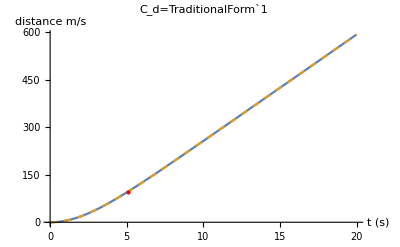

```mathematica
Plot[{Evaluate[y[t]/.s],Log[Cosh[√a √b t]]/a/.{a->  1/(2 m) ρ AreaProj Cd, b-> g}},{t,0,20},PlotRange->All,PlotStyle->{Automatic,Dashed},
Epilog->{PointSize->Large,Red, Point[{t90,Log[Cosh[√a √b t90]]/a/.{a->   1/(2 m) ρ AreaProj Cd, b->  g}}]},

AxesLabel->{"t (s)","distance m/s"},PlotLabel->StringForm["C_d=``",Cd]]
```

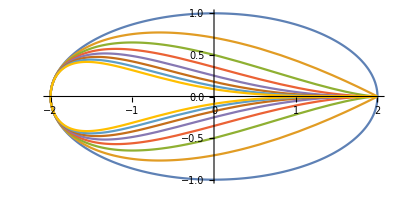

```mathematica
ParametricPlot[Evaluate[Table[{2Cos[t], Sin[t] Sin[t/2]^m},{m,0,7}]],{t,0,2π}]
```

## What speed do we have? from 20 m we are

```mathematica
Solve[height == -Log[1-Perct^2]/(2 a),Perct]
```

{{Perct→ConditionalExpression[-√(1-ⅇ^(-2 a height)),-π<-2 Im[a height]≤π]},{Perct→ConditionalExpression[√(1-ⅇ^(-2 a height)),-π<-2 Im[a height]≤π]}}

```mathematica
Cd=0.47;
√((2 m g)/(ρ AreaProj Cd)) √(1-ⅇ^(-2 a height))/.{height->25, a-> 1/(2 m) ρ AreaProj Cd}
```

21.0562

```mathematica
√(1-ⅇ^(-2 a height))/.{height->25, a-> 1/(2 m) ρ AreaProj Cd}
```

0.429091

```mathematica
Cd = 1;
√(1-ⅇ^(-2 a height))/.{height->25, a-> 1/(2 m) ρ AreaProj Cd}
√((2 m g)/(ρ AreaProj Cd))√(1-ⅇ^(-2 a height))/.{height->20, a-> 1/(2 m) ρ AreaProj Cd}
Cd = 0.47;
√(1-ⅇ^(-2 a height))/.{height->25, a-> 1/(2 m) ρ AreaProj Cd}
√((2 m g)/(ρ AreaProj Cd))√(1-ⅇ^(-2 a height))/.{height->20, a-> 1/(2 m) ρ AreaProj Cd}
Cd = 0.04;
√(1-ⅇ^(-2 a height))/.{height->25, a-> 1/(2 m) ρ AreaProj Cd}
√((2 m g)/(ρ AreaProj Cd))√(1-ⅇ^(-2 a height))/.{height->25, a-> 1/(2 m) ρ AreaProj Cd}
```

0.592796

18.2021

0.429091

19.0199

0.13103

22.0405

```mathematica
Cd= 0.47;
2 a height/.{ a-> 1/(2 m) ρ AreaProj Cd}
```

0.00813947 height

Velocity without air resistance

#### p=1/2 a t^2 t = √((2p)/a) v=a t v = √(2p a)

```mathematica
√(2p  g)/.p->20
```

19.799

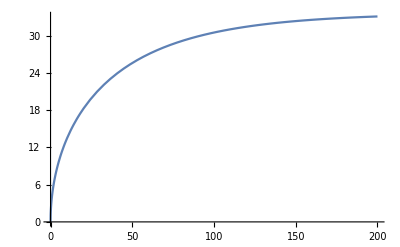

```mathematica
Plot[√((2 m g)/(ρ AreaProj Cd)) √(1-ⅇ^(-2 1/(2 m) ρ AreaProj Cd height)),{height,0,200}]
```